# Mysticeti Consensus Digital Twin

## Corrected, auditable educational direct-decision model

```mathematica
SeedRandom[42]; Get[FileNameJoin[{NotebookDirectory[], "src", "MysticetiModel.wl"}]]
```

## 1. Scope and claim status

EXACT means elementary equal-authority quorum arithmetic. FIXTURE means executable educational consistency evidence. CSV TRANSCRIPTION means consistency with the local paper transcription, not independent paper verification. SYNTHETIC means an uncalibrated sensitivity model. This is not the Sui implementation, a WAN simulation, a production prediction, or a complete protocol proof.

## 2. Slots, support, and authority counting

A slot is explicitly <|Validator -> v, Round -> r|>; every block in that slot is a proposal. SupportedProposal traverses ancestors breadth-first and sorts each frontier by {round, validator, ID}, selecting at most one proposal. Every threshold counts distinct validator authorities, so equivocations never add quorum weight.

```mathematica
Grid[Prepend[Table[{f, CommitteeSize[f], QuorumThreshold[f], HonestIntersectionLowerBound[CommitteeSize[f], QuorumThreshold[f], f]}, {f, 1, 5}], {"f", "n=3f+1", "q=2f+1", "honest intersection"}], Frame -> All]
```

f | n=3f+1 | q=2f+1 | honest intersection
1 | 4 | 3 | 1
2 | 7 | 5 | 1
3 | 10 | 7 | 1
4 | 13 | 9 | 1
5 | 16 | 11 | 1

## 3. Deterministic round DAG

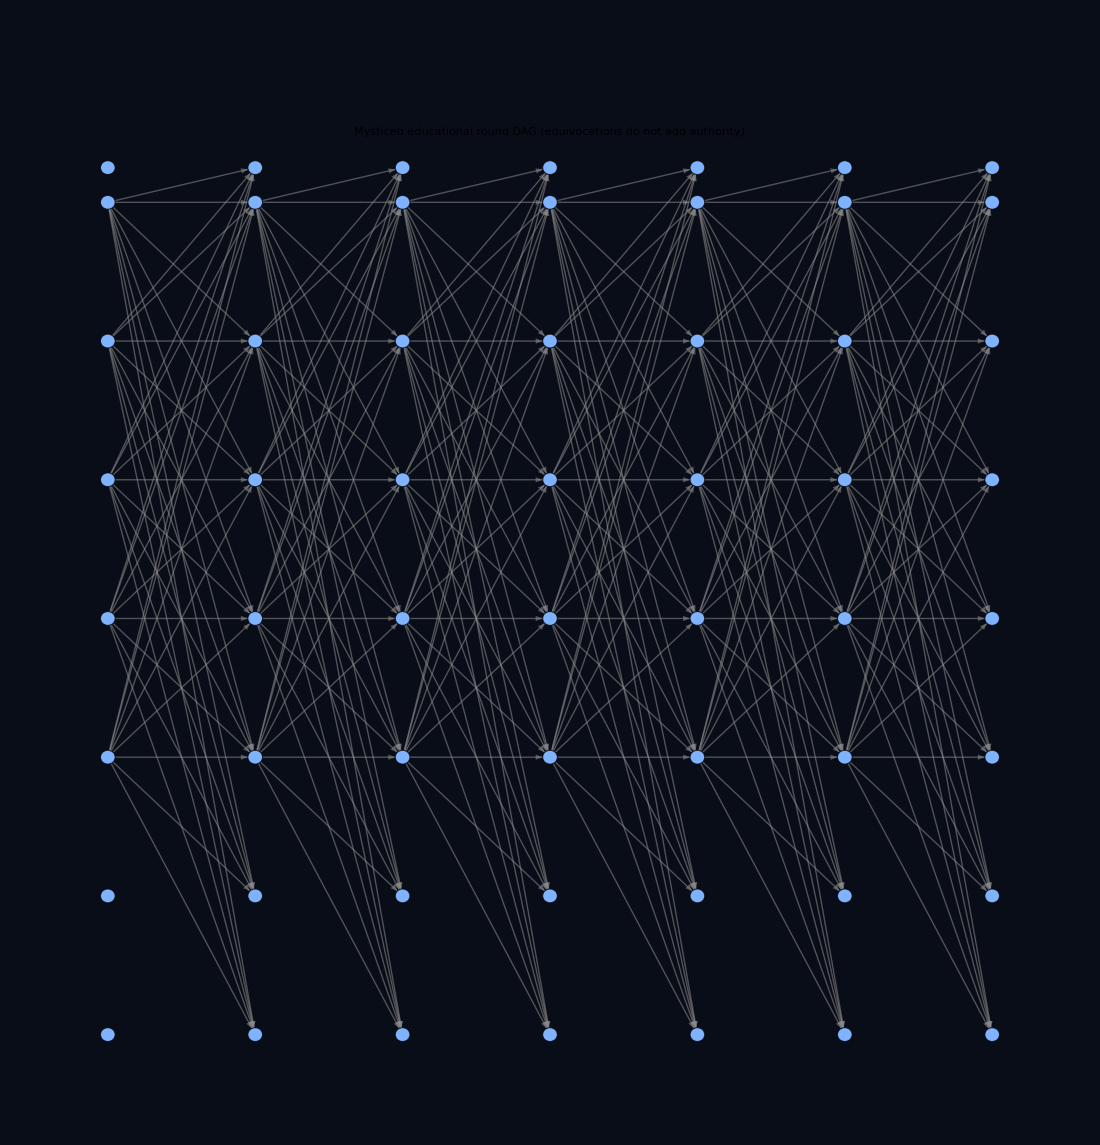

```mathematica
SeedRandom[42]; demoDAG = GenerateMysticetiDAG[<|"F" -> 2, "Rounds" -> 7, "Seed" -> 42, "ByzantineCount" -> 1, "Equivocation" -> True|>]; DAGVisualization[demoDAG]
```

Honest parent sets contain at most one prior-round block per authority. Equivocations remain visible but cannot inflate parent or decision thresholds.

## 4. Certificate versus direct commit

```mathematica
slot = <|"Validator" -> 1, "Round" -> 1|>; {SupportedProposal[demoDAG, "r2v2", slot], CertificateEvidence[demoDAG, "r1v1"], DirectSlotDecision[demoDAG, slot]}
```

{<|ID→r1v1,Validator→1,Round→1,Parents→{},Status→Byzantine,Crashed→False,Equivocation→False|>,{<|CertificateBlockID→r3v1,CertificateAuthority→1,SupporterAuthorities→{1,2,3,4,5},SupporterBlockIDs→{r2v1,r2v2,r2v3,r2v4,r2v5}|>,<|CertificateBlockID→r3v1e,CertificateAuthority→1,SupporterAuthorities→{5,4,3,2,1},SupporterBlockIDs→{r2v5,r2v4,r2v3,r2v2,r2v1}|>,<|CertificateBlockID→r3v2,CertificateAuthority→2,SupporterAuthorities→{1,2,3,4,5},SupporterBlockIDs→{r2v1,r2v2,r2v3,r2v4,r2v5}|>,<|CertificateBlockID→r3v3,CertificateAuthority→3,SupporterAuthorities→{1,2,3,4,5},SupporterBlockIDs→{r2v1,r2v2,r2v3,r2v4,r2v5}|>,<|CertificateBlockID→r3v4,CertificateAuthority→4,SupporterAuthorities→{1,2,3,4,5},SupporterBlockIDs→{r2v1,r2v2,r2v3,r2v4,r2v5}|>,<|CertificateBlockID→r3v5,CertificateAuthority→5,SupporterAuthorities→{1,2,3,4,5},SupporterBlockIDs→{r2v1,r2v2,r2v3,r2v4,r2v5}|>,<|CertificateBlockID→r3v6,CertificateAuthority→6,SupporterAuthorities→{1,2,3,4,5},SupporterBlockIDs→{r2v1,r2v2,r2v3,r2v4,r2v5}|>,<|CertificateBlockID→r3v7,CertificateAuthority→7,SupporterAuthorities→{1,2,3,4,5},SupporterBlockIDs→{r2v1,r2v2,r2v3,r2v4,r2v5}|>},<|Decision→Commit,Pattern→q distinct r+2 certificate authorities,Slot→<|Validator→1,Round→1|>,Proposal→r1v1,SupporterAuthorities→{1,2,3,4,5,6,7},CertificateAuthorities→{1,2,3,4,5,6,7},CertificateIDs→{r3v1,r3v1e,r3v2,r3v3,r3v4,r3v5,r3v6,r3v7},SkipAuthorities→<||>,Threshold→5|>}

An r+2 block is a certificate block for P only when its r+1 parents include q distinct authorities whose SupportedProposal is P. A direct commit additionally requires q distinct r+2 certificate-block authorities for that same P. One certificate is not a commit.

## 5. Direct skip

Skip evidence is at r+1: for every observed proposal in the slot, q distinct observed r+1 authorities do not support it; with no proposal, q observed r+1 authorities support no proposal. Otherwise the result remains Undecided. This is the conservative educational Section II-C direct pattern.

## 6. Consensus Safety Microscope

```mathematica
Manipulate[Module[{p, d, decision, margin}, SeedRandom[seed]; p = <|"F" -> f, "Rounds" -> rounds, "Seed" -> seed, "CrashCount" -> crashes, "Equivocation" -> equiv, "ByzantineCount" -> If[equiv, 1, 0]|>; d = GenerateMysticetiDAG[p]; decision = DirectSlotDecision[d, <|"Validator" -> 1, "Round" -> 1|>]; margin = HonestIntersectionLowerBound[d["CommitteeSize"], d["Quorum"], f]; Column[{Style["CONSENSUS SAFETY MICROSCOPE", 22, RGBColor[0.1, 0.8, 1]], DAGVisualization[d], Grid[{{"Honest overlap bound", margin}, {"Decision", decision["Decision"]}, {"Threshold", decision["Threshold"]}, {"Certificate IDs", Lookup[decision, "CertificateIDs", {}]}, {"Skip authorities", Lookup[decision, "SkipAuthorities", <||>]}}, Frame -> All]}]], {{f, 2}, 1, 4, 1}, {{crashes, 0}, 0, 4, 1}, {{rounds, 7}, 4, 10, 1}, {{equiv, True}, {False, True}}, {{seed, 42}, 1, 100, 1}]
```

## 7. Uncalibrated synthetic timing sensitivity

```mathematica
SeedRandom[42]; sim = SimulateMysticeti[<|"F" -> 3, "Rounds" -> 9, "Seed" -> 42, "BaseDelayMS" -> 120., "JitterMS" -> 40., "CrashCount" -> 1, "SyntheticSamples" -> 500|>]; KeyTake[sim, {"SyntheticSamples", "P50Milliseconds", "P95Milliseconds", "InvariantChecks", "ScientificLabel", "TimingAssumptions"}]
```

<|SyntheticSamples→500,P50Milliseconds→405,P95Milliseconds→520,InvariantChecks→<|ParentReferencesExist→True,DistinctParentAuthorities→True,HonestDistinctParentAuthorities→True|>,ScientificLabel→uncalibrated synthetic sensitivity model,TimingAssumptions→500 seeded samples by default; latency=max(1,3*base delay + sum of three Gaussian message-delay perturbations + 45 ms/crash + 25 ms/Byzantine). Not a WAN simulation or production prediction.|>

The formula is max(1, 3 base delays + three independent Gaussian perturbations + 45 ms per crash + 25 ms per Byzantine authority), using at least 250 seeded samples. Three message delays represent the proposal, supporter, and certificate/decision progression. Parameters are uncalibrated; outputs are neither WAN simulation nor production prediction.

## 8. Safety envelope and sensitivity frontier

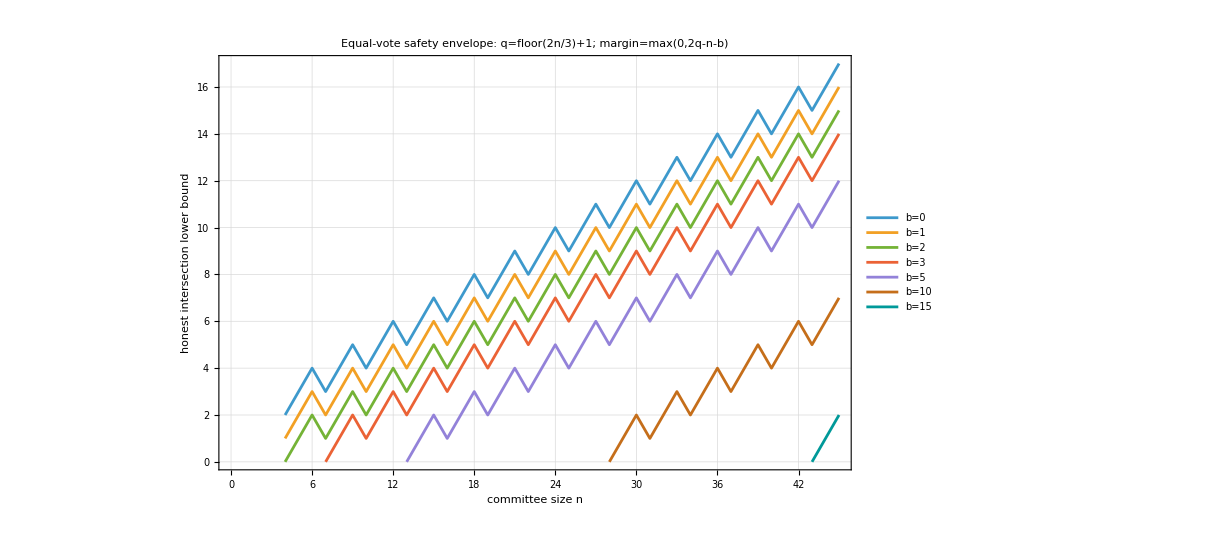

```mathematica
SafetyEnvelopePlot[]
```

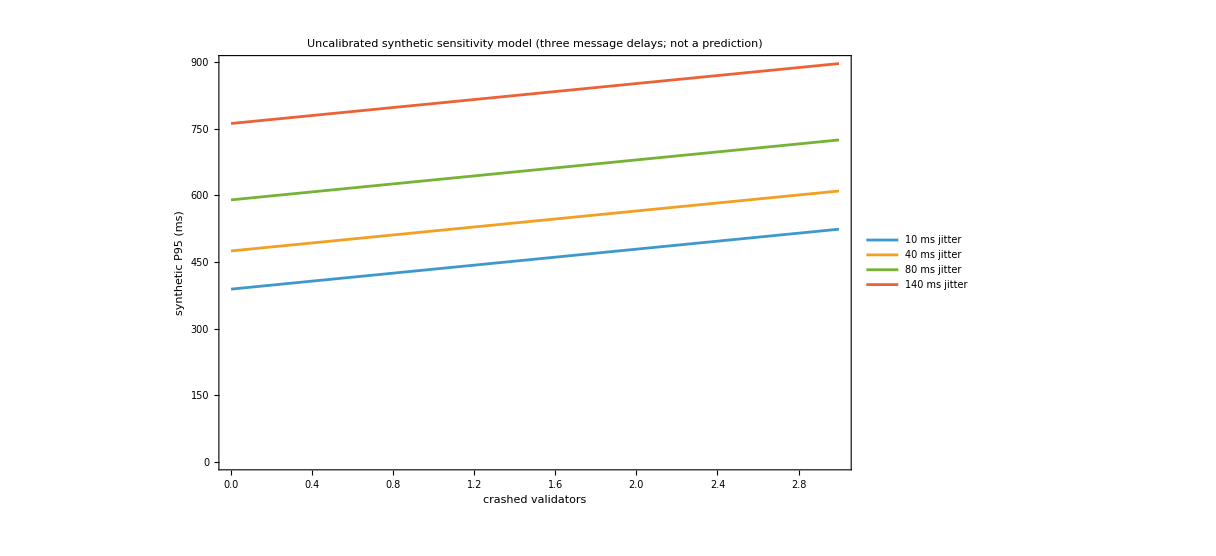

```mathematica
FaultFrontierPlot[]
```

SafetyEnvelopePlot uses explicit {CommitteeSize, HonestIntersection} pairs grouped by Byzantine count. The frontier is only the uncalibrated synthetic sensitivity model.

## 9. Production CSV fixture

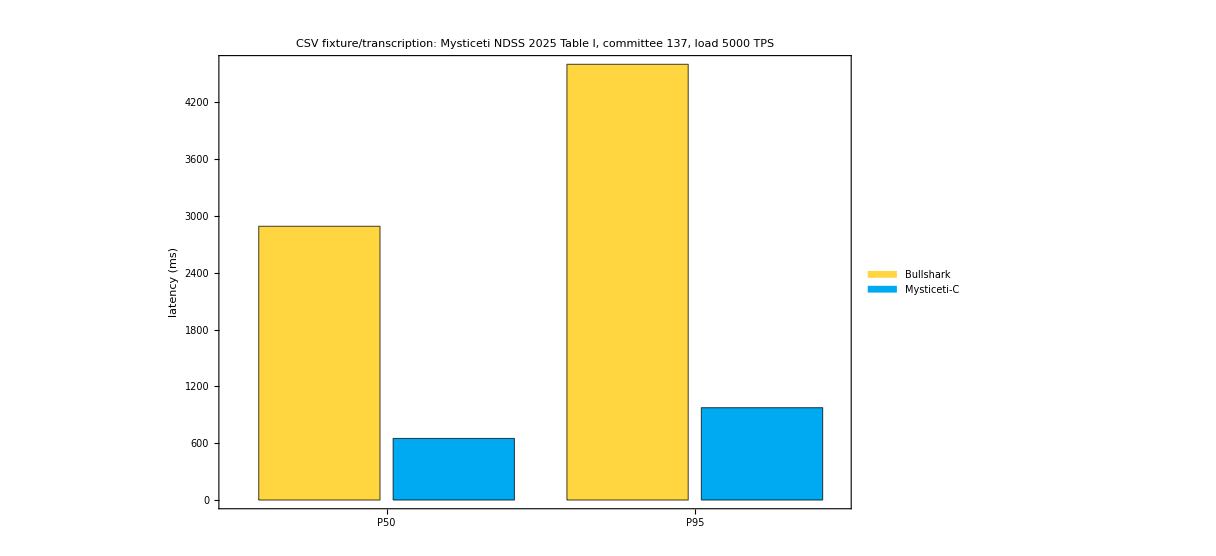

```mathematica
ProductionComparisonPlot[]
```

The plot imports data/paper_production_benchmark.csv. Checks compare expected fields and latency ratios to that imported transcription. This is fixture/transcription consistency, not independent paper verification.

## 10. Executable fixture checks

```mathematica
RunValidationSuite[]
```

<|Passed→12,Failed→0,AllPassed→True,Checks→<|FullSupportAndCertificatesCommit→True,FewerThanQCertificateAuthoritiesUndecided→True,QMinusOneSupportAuthoritiesUndecided→True,QNonSupportAuthoritiesSkip→True,DuplicateAuthorEquivocationDoesNotIncreaseCount→True,SupportedProposalDeterministicallySelectsOne→True,DeterministicReplay→True,ParentReferencesExist→True,DistinctParentAuthorities→True,CSVFixtureTranscriptionConsistency→True,CSVFixtureRatioConsistency→True,SyntheticSampleFloor→True|>,Scope→Educational equal-authority fixtures and CSV transcription consistency; not independent paper verification or complete protocol/Lean proof.|>

Fixtures cover full support plus q certificates -> Commit; fewer than q certificate authorities -> Undecided; q-1 supporters -> Undecided; q non-support authorities -> Skip; duplicate-author equivocation; deterministic single-valued support; deterministic replay; parent existence and distinct-parent authorities; CSV rows/ratios; and the synthetic sample floor.

## 11. Verification scope and limitations

The companion Lean 4 project kernel-checks quorum intersection, honest overlap, same-slot certificate uniqueness, and the conflicting-transaction quorum core. Run build_all.ps1 for the combined release gate. Lean does not verify this Wolfram implementation or the complete protocol. Limitations include equal voting power rather than stake, deterministic parent selection, round-level observations, no full Mysticeti state machine, no indirect decision path, no epoch/GC/synchronization/cryptography model, and no complete safety or liveness theorem.

## 12. KEY FINDINGS

KEY FINDINGS
- Direct commit requires q distinct r+2 certificate authorities, and each certificate requires q distinct r+1 supporter authorities for one proposal.
- Direct skip evidence is counted at r+1.
- Deterministic support chooses at most one proposal per block and explicit slot.
- Equivocations are inspectable but never duplicate authority weight.
- Lean kernel-checks the equal-authority quorum core independently of Wolfram.
- Timing outputs are a seeded, uncalibrated synthetic sensitivity model with three message delays.
- CSV checks establish transcription consistency only; complete protocol correctness remains outside scope.